```mathematica
data=Flatten@Import["C:\\Users\\Sebastian\\Dropbox\\Studie\\Kurser\\Datalogi\\PCSD\\Assignments\\1\\tex\\lots-of-clients_100reqs_zipf0.5.txt","TSV"];
```

```mathematica
fancyData=Nest[
Module[{
nums=TakeWhile[#[[1,2;;]],IntegerQ]
},{
#[[1,(2+Length@nums);;]],
Append[#[[2]],nums]
}]&,{data,{}},25][[2]];
```

```mathematica
latencyData={Length[#],Total[#]/(100*Length[#])}&/@fancyData//N
```

{{1.,6.75},{2.,9.795},{3.,22.2433},{4.,11.835},{5.,10.468},{6.,33.5867},{7.,28.0443},{8.,24.805},{9.,23.0111},{10.,22.086},{11.,21.4582},{12.,20.0092},{13.,21.6123},{14.,22.9714},{15.,25.872},{16.,29.3063},{17.,26.1729},{18.,21.9733},{19.,26.5826},{20.,42.8115},{21.,129.748},{22.,84.4132},{23.,84.973},{24.,63.5113},{25.,71.9116}}

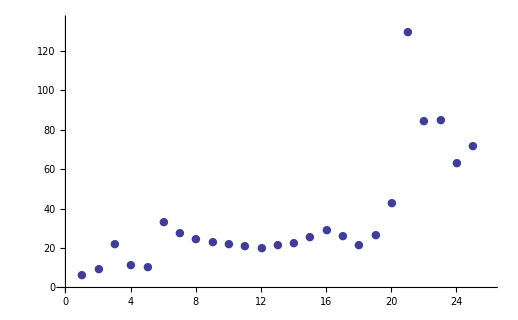

```mathematica
ListPlot[latencyData,PlotRange->{{0,26},{0,135}},PlotMarkers->{Automatic,Small}]
```

```mathematica
throughputData={Length[#],(100*Length[#])/(Total[#]/1000)}&/@fancyData//N
```

{{1.,148.148},{2.,102.093},{3.,44.9573},{4.,84.4951},{5.,95.5292},{6.,29.7737},{7.,35.6579},{8.,40.3145},{9.,43.4573},{10.,45.2776},{11.,46.6023},{12.,49.9771},{13.,46.2699},{14.,43.5323},{15.,38.6518},{16.,34.1224},{17.,38.2074},{18.,45.5097},{19.,37.6185},{20.,23.3582},{21.,7.70724},{22.,11.8465},{23.,11.7684},{24.,15.7452},{25.,13.906}}

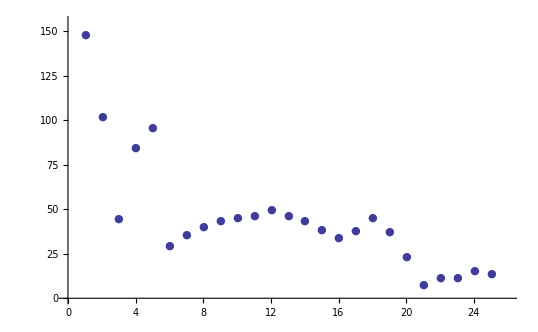

```mathematica
ListPlot[throughputData,PlotRange->{{0,26},{0,155}},PlotMarkers->{Automatic,Small}]
```